```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
(*Params*)
l=1;
m=1;
k=1;
M=1;
a =.998M;
r0=10M;
θi = π/3;
xi = Cos[θi];

Δ[r_]:=r^2-2M r+a^2;
```

```mathematica
(*Frequencies wrt BL time*)
Freqs = KerrGeoFrequencies[a,r0,0,xi];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];
ω = m Ωϕ+ k Ωθ;
```

0.0618444

```mathematica
(*Toolkit computes orbit parameterised by λ (Mino time), so we need to switch our integration variable*)
dtdλ[θ_]:=ℰ(((r0^2+a^2)^2)/Δ[r0]-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/Δ[r0]);
Υθ=KerrGeoFrequencies[a,r0,0,xi,Time->"Mino"][[2]];
Λθ = (2π)/Υθ;
```

1.75597

```mathematica
Consts = KerrGeoConstantsOfMotion[a,r0,0,xi];
ℰ=Consts[[1]];
ℒ=Consts[[2]];
Q = Consts[[3]];
```

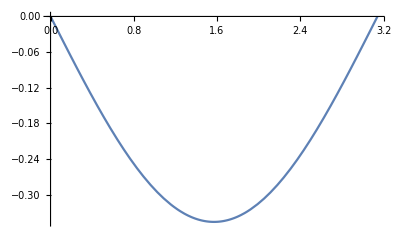

```mathematica
S[θ_]:=SpinWeightedSpheroidalHarmonicS[0,l,m,a ω, θ,0];
Plot[S[θ],{θ,0,π}]
```

```mathematica
orbit=KerrGeoOrbit[a,r0,0,xi];
{tp,rp,θp,ϕp}=orbit["Trajectory"];
ParametricPlot3D[{√(rp[λ]+a^2)Sin[θp[λ]]Cos[ϕp[λ]],√(rp[λ]+a^2)Sin[θp[λ]]Sin[ϕp[λ]],√(rp[λ]+a^2)Cos[θp[λ]]},{λ,0,20Λθ}]
```

ParametricPlot3D::exclul: {(1-3/4 JacobiSN[1.00132 Plus[«2»],0.00527414]^2)-0,3/4 JacobiSN[1.00132 (Times[«2»]+Times[«2»]),0.00527414]^2-1,0.00527414 JacobiSN[1.00132 (Times[«2»]+Times[«2»]),0.00527414]^2-1,JacobiCN[1.00132 (π/2+3.57818 λ),0.00527414]-0,Cos[0.248877 (0.+5.63547 Im[λ])]-0,«13»-0,Sin[0.248877 (0.+4.01805 («1»))]-0,Sin[0.248877 (0.+4.01805 (Times[«2»]+Times[«2»]))]-0,Sin[0.248877 (0.+4.01805 (Times[«2»]+Times[«2»]))]-0,-3/4 Im[JacobiSN[1.00132 Plus[«2»],0.00527414]^2]-0,«4»} must be a list of equalities or real-valued functions.

-Graphics3D-

```mathematica
(*Calculating 4 velocity*)
gtt[M_,a_,r_,θ_]:=-((a^4+2 r^4+a^2 r (2 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ])/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ])))
gtϕ[M_,a_,r_,θ_]:=-(4 a M r)/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]))
ut[M_,a_,r_,θ_,ℰ_,ℒ_]:=gtϕ[M,a,r,θ]ℒ-gtt[M,a,r,θ]ℰ
```

```mathematica
-(2 Ωθ)/r0 NIntegrate[S[θp[λ]]/ut[M,a,r0,θp[λ]] Cos[ω tp[λ]-m ϕp[λ]]dtdλ[θp[λ]],{λ,0,Λθ}]
```

Dot::dotsh: Tensors {-0.367602,0.0229687,-0.000857574,0.0000236625,-5.23889×10^-7,9.73366×10^-9,-1.56182×10^-10,2.20829×10^-12,-2.79312×10^-14,3.19707×10^-16,«1»} and {1.,2.,4.,8.,16.,32.,64.,128.,256.,512.,«2»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)/ut[1,0.998,10,ArcCos[1/2 √3 JacobiSN[1.00132 Plus[«2»],0.00527414]]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.75597}}.

-0.0060108 NIntegrate[(S[θp[λ]] Cos[ω tp[λ]-m ϕp[λ]] dtdλ[θp[λ]])/ut[M,a,r0,θp[λ]],{λ,0,Λθ}]

Cos[ξ]